```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/examples/binary_tree_simple_test/tree_structure.dat"]
```

{{6,2,8},{2,1,4},{8,7,8},{1,1,1},{4,2,4},{7,6,8},{8,8,9}}

```mathematica
maybeP=Except[n]|n
binaryTreeNodeP={Except[n],maybeP,maybeP}

childOrEmptyNode[value:Except[n],n,side:(left|right)]:="empty"<>ToString[value]<>ToString[side]
childOrEmptyNode[Except[n],child:Except[Nothing],(left|right)]:=child

binaryTreeNodeEdges[{v:Except[n],l:maybeP,r:maybeP}]:={v->childOrEmptyNode[v,l,left],v->childOrEmptyNode[v,r,right]}
makeBinaryTree[nodes:{binaryTreeNodeP..}]:=Flatten[Map[binaryTreeNodeEdges,nodes]]

removeEmptyEdges=(If[!StringMatchQ[ToString[#2[[2]]],"empty"~~__],{Darker[Red],Arrowheads[{{Medium,0.5}}],Arrow[#1]}]&)
removeEmptyVertices=(If[!StringMatchQ[ToString[#2],"empty"~~__],{Background->LightYellow,Inset[Framed[#2],#1]}]&)
```

Except[n]|n

{Except[n],Except[n]|n,Except[n]|n}

If[!StringMatchQ[ToString[#2⟦2⟧],empty~~__],{Darker[Red],Arrowheads[{{Medium,0.5}}],Arrow[#1]}]&

If[!StringMatchQ[ToString[#2],empty~~__],{Background→LightYellow,Inset[#2,#1]}]&

{{1,2,6},{2,3,4},{6,7,n},{4,n,5}}

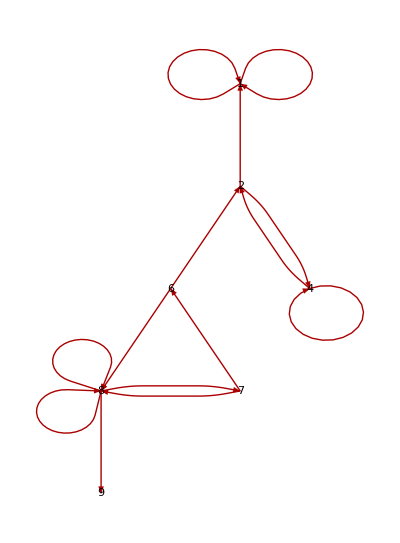

```mathematica
nodes={{1,2,6},{2,3,4},{6,7,n},{4,n,5}}
TreePlot[makeBinaryTree[data],Top,1,VertexRenderingFunction->removeEmptyVertices,EdgeRenderingFunction->removeEmptyEdges]
```